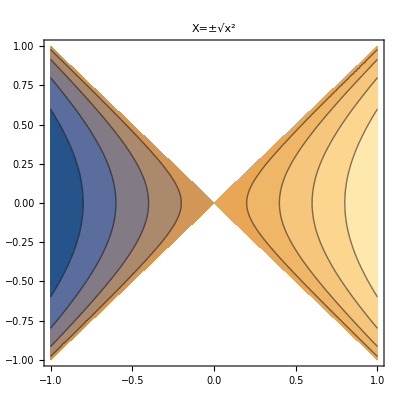
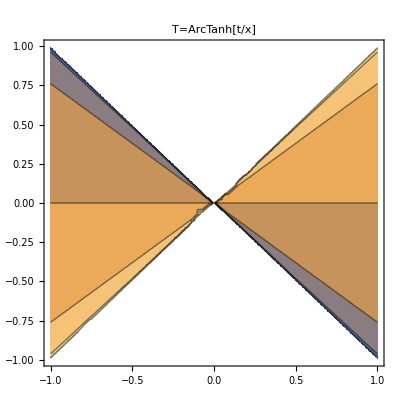

```mathematica
{ContourPlot[{Piecewise[{{-√(x^2-t^2), x<0}, {√(x^2-t^2), True}}]},{x,-1,1},{t,-1,1},AspectRatio->Automatic,PlotLabel->"X=±√(x^2)"],ContourPlot[{ArcTanh[t/x]},{x,-1,1},{t,-1,1},AspectRatio->Automatic,PlotLabel->"T=ArcTanh[t/x]"]}
```

```mathematica
DSolve[X^2 ϕ''[X]+X ϕ'[X]+W^2 ϕ[X]==0,ϕ[X],X]
```

{{ϕ[X]→C[1] Cos[W Log[X]]+C[2] Sin[W Log[X]]}}

```mathematica
-Abs[κ]T+κ/a Log@(X/X0)
ⅇ^(ⅈ%/.{X->√(x^2-t^2),T->1/a ArcTanh[t/x]})//TrigToExp;
{Simplify[%,Assumptions->x>t&&x>-t&&x>0&&X0>0&&a>0],Simplify[%,Assumptions->x<t&&x<-t&&x<0&&X0>0&&a>0]}
```

-T Abs[κ]+(κ Log[X/X0])/a

{((-t+x)/(t+x))^((ⅈ Abs[κ])/(2 a)) ((√(-t^2+x^2))/X0)^((ⅈ κ)/a),((-t+x)/(t+x))^((ⅈ Abs[κ])/(2 a)) ((√(-t^2+x^2))/X0)^((ⅈ κ)/a)}

```mathematica
Abs[κ]T-κ/a Log@(X/X0)
ⅇ^(ⅈ%/.{X->√(x^2-t^2),T->1/a ArcTanh[t/x]})//TrigToExp;
{Simplify[%,Assumptions->x>t&&x>-t&&x>0&&X0>0&&a>0],Simplify[%,Assumptions->x<t&&x<-t&&x<0&&X0>0&&a>0]}
```

T Abs[κ]-(κ Log[X/X0])/a

{((-t+x)/(t+x))^(-(ⅈ Abs[κ])/(2 a)) ((√(-t^2+x^2))/X0)^(-(ⅈ κ)/a),((-t+x)/(t+x))^(-(ⅈ Abs[κ])/(2 a)) ((√(-t^2+x^2))/X0)^(-(ⅈ κ)/a)}

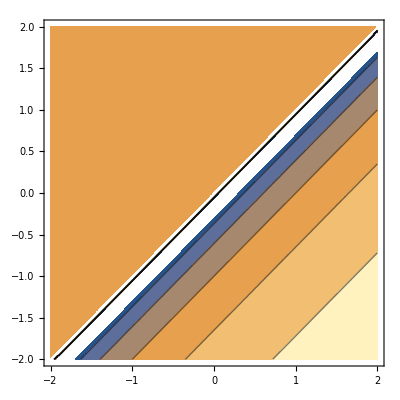
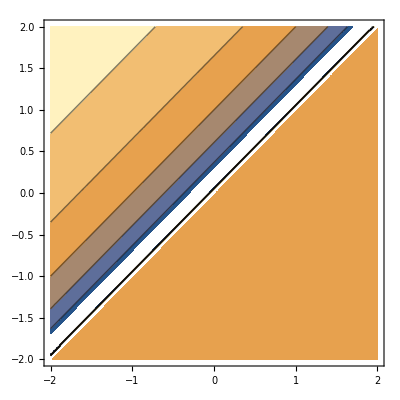

```mathematica
ϕ1p[x_,t_]:=Piecewise[{{ⅇ^(ⅈ Log[x-t]), x>t}, {0, True}}]
ϕ2m[x_,t_]:=Piecewise[{{ⅇ^(ⅈ Log[t-x]), x<t}, {0, True}}]
ContourPlot[#,{x,-2,2},{t,-2,2}]&/@{Arg@ϕ1p[x,t],Arg@ϕ2m[x,t]}
```

Piecewise[{{(t-x)^ⅈ, t>x}, {(-t+x)^ⅈ, t<x}, {0, True}}]

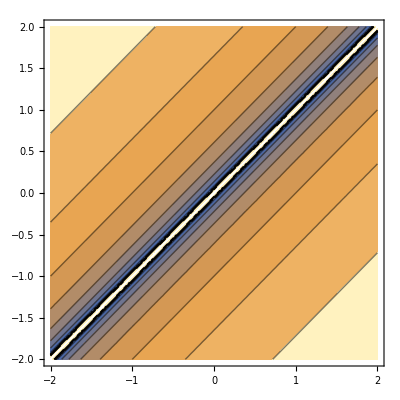

```mathematica
ϕ1p[x,t]+ϕ2m[x,t]//FullSimplify
ContourPlot[Arg[%],{x,-2,2},{t,-2,2}]
```